```mathematica
d=-0.12; mu2=0.175; t=0.4; c=6.25;a1=0.00125; G1=0.00086; b=0.0004138;
F6[x_,U_]:=√(d^2+U^2+(c*x)^2+t^2/2-√((t^2+4*U^2)*(c*x)^2+4*U^2*d^2+2*t^2*d*U+t^4/4));

Framed[Manipulate[Plot[{F6[x,U],0.225},{x,-0.15,0.15},PlotRange->{0,0.5}],{U,0,0.16},Alignment->{Right,Right},ContentSize->{400,400}],RoundingRadius->20]
```

```mathematica
f1[x_,U_]:=√(d^2+U^2+(c*x)^2+t^2-2*√((t^2+U^2)*(c*x)^2+U^2*d^2));
Framed[Manipulate[Plot[{f1[x,U],0.41},{x,-0.15,0.15},PlotRange->{0,0.5}],{U,0,0.235},Alignment->{Right,Right},ContentSize->{400,400}],RoundingRadius->20]
```

```mathematica
Plot[{F6[x,0.10],F6[x,0.14],F6[x,0.165],0.225},{x,-0.1,0.1},FrameLabel->{"k,Å^-ı","E, eV"},PlotRange->{0.15,0.5},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Green},{Thickness[0.003],Blue},{Thickness[0.003],Black, Dashed}},Epilog->{{Black,Text["U = 100  meV",{0.032,0.45},{-1,-1}]},{Black,Text["U = 140 meV",{0.032,0.42},{-1,-1}]},{Black,Text["U = 165 meV",{0.032,0.39},{-1,-1}]}},Frame->True]
```

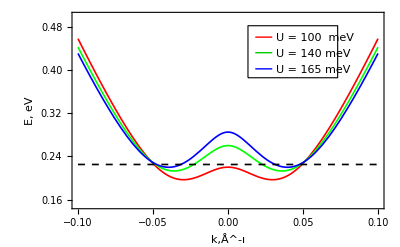

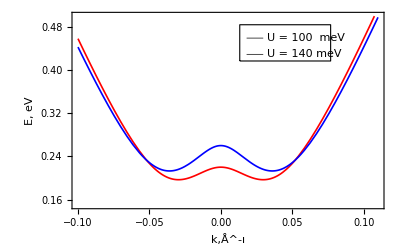

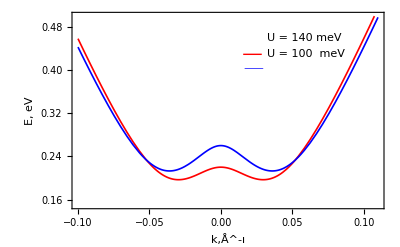

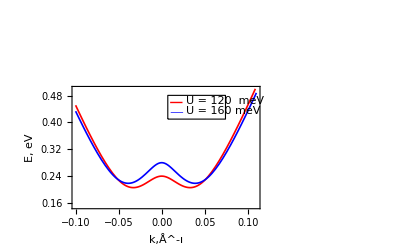

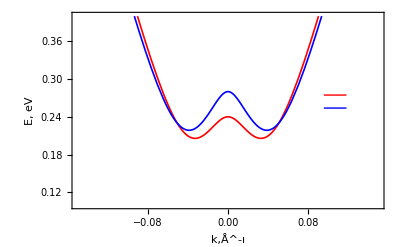

```mathematica
Plot[{f1[x,0.120],f1[x,0.225],0.404},{x,-0.15,0.15},FrameLabel->{"k,Å^-ı","E, eV"},PlotRange->{0.08,0.55},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Black,Dashed}},Epilog->{{Black,Text["U = 120  meV",{0.048,0.495},{-1,-1}]},{Black,Text["U = 225 meV",{0.048,0.455},{-1,-1}]}},Frame->True]
```